Physical Constants:

```mathematica
m=1;ω=1;ℏ=1;
```

Numerical Constants:

```mathematica
Nx=100;xmin=-10.;xmax=10.;dx=(xmax-xmin)/(Nx+1);Nt=100;dt=(2π/Ω)/Nt;
```

### Construct H

Identity Matrix:

```mathematica
OpenOne=SparseArray[{i_,i_}->1.,{Nx,Nx}];
```

Second Derivative Operator:

```mathematica
D2=1.0/dx^2 SparseArray[{{i_,i_}->-2.,{i_,j_}/;Abs[i-j]==1->1.},{Nx,Nx}];
```

Position Operator:

```mathematica
X=SparseArray[{i_,i_}->xmin+dx i,{Nx,Nx}];
```

The Hamiltonian:

```mathematica
H=-1/2 D2+1/2 X.X;
```

```mathematica
Take[Reverse[Eigenvalues[H]],2]
```

{0.498772,1.49385}

```mathematica
EVE=Eigenvectors[H]/Sqrt[dx];
```

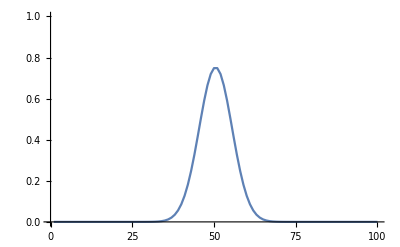

```mathematica
ListLinePlot[EVE[[100]],PlotRange->{0,1}]
```

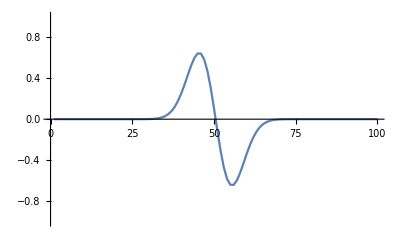

```mathematica
ListLinePlot[EVE[[99]],PlotRange->{-1,1}]
```

### Construct U

Denominator in Cayley’s Form:

```mathematica
Uplus=OpenOne+1/2 I H dt;
```

Numerator in Cayley’s Form:

```mathematica
Uminus=OpenOne-1/2 I H dt;
```

### Solving the TDSE

The ground and first excited states and the wave function at t=0:

```mathematica
ψ0=Eigenvectors[H][[Nx]]/Sqrt[dx];
```

```mathematica
ψ1=Eigenvectors[H][[Nx-1]]/Sqrt[dx];
```

```mathematica
Psi0=(ψ0+ψ1)/Sqrt[2];
```

Analytical form of eigenstates:

```mathematica
psi[n_,x_]:=((m ω)/(π ℏ))^(1/4)1/(√(2^n n!))HermiteH[n,√((m ω)/ℏ)x]Exp[-1/2(√((m ω)/ℏ)x)^2]
```

```mathematica
Psi=Psi0;
```

```mathematica
Data=Table[(*Step the wave function forward in time*)
Psi=LinearSolve[Uplus,Uminus.Psi];
If[(*Only Plot 100 frames regardless of number of time steps*)
Mod[i,Nt/100]==0,
(*The exact solution. Minus sign is due to different sign convention in numeric/analytic states*)
g[x_]=(psi[0,x]Exp[-I ω(i dt)/2]-psi[1,x]Exp[-3 I ω(i dt)/2])/Sqrt[2];
(*Plotting commands*)
Show[{Plot[{Re[g[x]],Im[g[x]],Abs[g[x]]},{x,-3,3},PlotRange->{-1,1},AxesLabel->{"x","|Ψ|"},PlotStyle->{Blue,Red,Black}],ListPlot[{Re[Psi],Im[Psi],Abs[Psi]},PlotRange->{-1,1},DataRange->{xmin+dx,xmax-dx},PlotStyle->PointSize[Medium]]}],Nothing],{i,1,Nt}];
```

```mathematica
ListAnimate[Data]
```